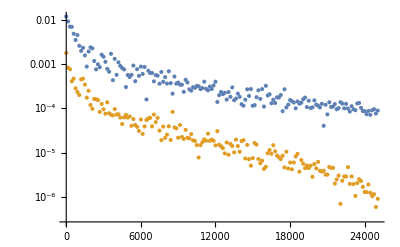
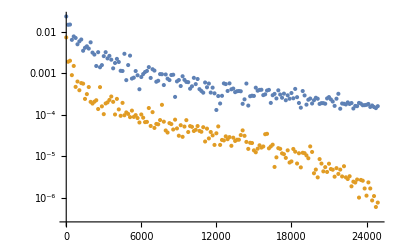
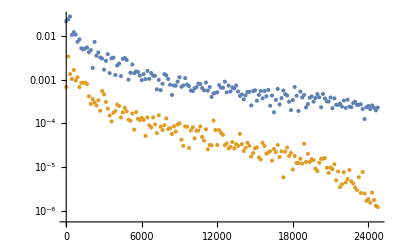
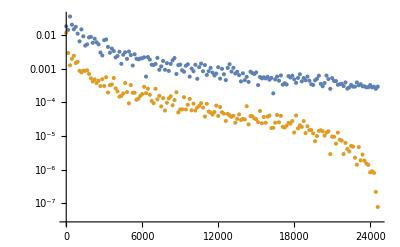
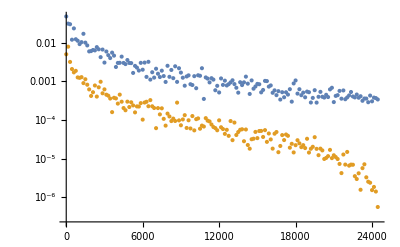
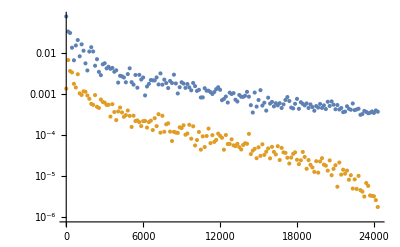
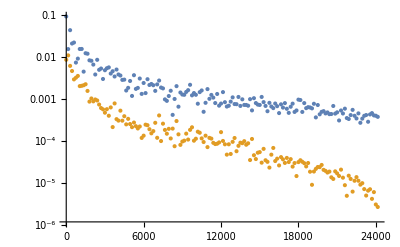
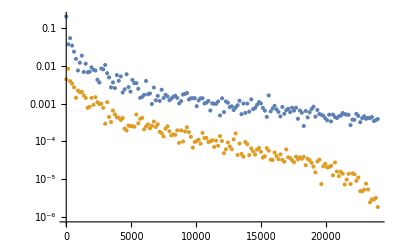

```mathematica
(* CHARTWALLS CORRECTION *) 

(* these charts show mean squared error over for different window sizes*) 
(data = getRfFprMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)40, (*win size *) #, (* bin width *)150];
ListLogPlot[{data[[All,{1,3}]], data[[All,{1,4}]]}, PlotRange->All])&/@ Range[1,30](* should be 1 & 29! *)
```